# Kauffman Polynomials of Pretzel Knots

By Raphael Walker

Making use of Lu and Zhong’s formula for the Dubrovnik Polynomial and Lickorish’s relation between the Dubrovnik polynomial and the L-polynomial. In the various functions we will define, q is assumed to be a list of twist numbers referring to the Pretzel knot $P(q_1, ... q_n)$.

### Lu and Zhong’s Dubrovnik Polynomial

Lu and Zhong define the Dubrovnik polynomial of the unknot to be $\delta$ rather than 1. It is trivial to undo this by simply dividing the resulting polynomial by $\delta$. Moreover, they replace $z$ by $s - s^{-1}$. While this substitution is mathematically invertible, it is no simple matter to do it computationally. We achieve this by solving the equation $z = s - s^{-1}$ for $s$, substituting in this value, and letting Mathematica handle the simplification.

First we define some shorthand, and write out the base change matrix.

```mathematica
ai := 1/a;
si := 1/s;
d   := (a - ai)/(s - si) + 1;
di := 1/d;
M   = {
{(si - di*si - di*ai)/(s + si), (-si - di*s + di*ai)/(s + si), di},
{(-s - di*si - di*ai)/(s + si), (s - di*s + di*ai)/(s + si), di},
{(si*d + a - di*si - di*ai)/(s +si), (s*d - a - di*s + di*ai)/(s+si), di}};
```

Now we can write out the computation for the Lu-Zhong polynomial.

```mathematica
LuZhong[q_] :=
	d * M⟦3⟧ . Table[Times@@(M⟦j⟧ . {s,-si,ai}^#1&)/@q,{j,3}]
```

### Dubrovnik Polynomial

We want to convert from the Lu-Zhong form of the Dubrovnik polynomial to the standard one. To do this, we need to rewrite the equation in the variables $a, z$ where $z = s - s^{-1}$.

```mathematica
Dubrovnik[q_] :=
	LuZhong[q] /. Solve[z == s-si,s][[1]] // Simplify
```

### Kauffman

Now we will normalize the Dubrovnik polynomial to get the Kauffman Y polynomial. But first, we need the writhe. For the family we are interested in, the writhe is easy to compute.

```mathematica
Writhe[{3, -3, n_}] := -n
```

Now we can finally compute the Kauffman polynomial.

```mathematica
Kauffman[q_] :=
	Simplify[Dubrovnik[q]*ai^Writhe[q]]
```

## Thurston-Bennequin number

We can use the Kauffman polynomial to get an upper bound on the maximal Thurston-Bennequin number. In the form of the polynomial that we have, this bound is the minimal degree of a.

```mathematica
TBBound[q_] :=
	(Exponent[Kauffman[q], a, Max]* -1)//Simplify
```

```mathematica
$Assumptions = {n ∈ Integers};
TBBound[{3, -3, n}]
```

-Max[1,4+n]

Let us check to make sure that the coefficients of a^(n-4) or a^(-1) are never identically zero.

```mathematica
p = Assuming[n ∈ Integers,{3, -3, n}//Kauffman//Expand//PowerExpand//Apart//Expand];
coeff1 = Assuming[n ∈ Integers, Coefficient[p, a,1]//FullSimplify]
Solve[coeff1==0,n]//Simplify
```

1/z

{}

So certainly the coefficient of a^(-1) is never zero. How about a^(n-4)?

```mathematica
coeff = Assuming[n ∈ Integers, Coefficient[p, a,n+4]//FullSimplify]
Solve[coeff==0,n]
```

1/(2 z √(4+z^2))(-z+√(4+z^2))^-n (2^(1+n) z √(4+z^2)+2^n z^3 √(4+z^2)+2^n (2+4 z^2+z^4)+2 z √(4+z^2) (-2+z (-z+√(4+z^2)))^n+z^3 √(4+z^2) (-2+z (-z+√(4+z^2)))^n-(2+4 z^2+z^4) (-2+z (-z+√(4+z^2)))^n)

{{n→ConditionalExpression[(-2 ⅈ π C[1]-Log[1/2 (2+16 z^2+20 z^4+8 z^6+z^8+4 z √(4+z^2)+10 z^3 √(4+z^2)+6 z^5 √(4+z^2)+z^7 √(4+z^2))])/(Log[2]-Log[-2+z (-z+√(4+z^2))]), ]}}

The only way the coefficient could be identically zero would be if the expression for n evaluated to an integral constant. The graph below shows that it does not.

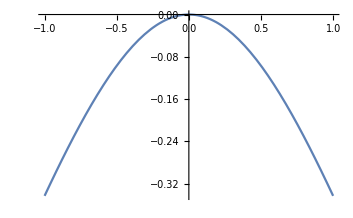

```mathematica
n[z_] := Log[1/2 (2+16 z^2+20 z^4+8 z^6+z^8+4 z √(4+z^2)+10 z^3 √(4+z^2)+6 z^5 √(4+z^2)+z^7 √(4+z^2))]/Log[1/2 (-2-z^2+z √(4+z^2))]
Plot[Re[n[z]], {z, -1, 1}]
```

Thus the minimum degree of a in the Kauffman polynomial of the pretzel knot P (3, -3, n) is min (-1, n - 4) and so the maximal TB of the pretzel knot P (3, -3, n) is min (-1, n - 4) , as this bound is sharp for this family of pretzel knots.